## 1. 问卷数据导入与品质分析

问卷通过”问卷星”在线问卷托管平台进行设计, 发布以及答卷管理. 在2024-10-15 0时许开始对外接收, 至2024-10-21 24时停止收集. 
受访者通过网页查看问卷内容并提交答案.

### 1.1. 问卷Excel导入为Mathematica的嵌套List函数式

```mathematica
ansRaw=Import[NotebookDirectory[]<>"285334255_00001-00078.xlsx","XLSX"]//First;
```

```mathematica
ansRaw//Dimensions
```

{79,105}

共计收集78份问卷(Excel第一行为表头, 用于声明字段的名称).

Excel每列字段名称提取

```mathematica
ansFields=ansRaw[[1,All]];
MapIndexed[{#2[[1]],#1}&,ansFields]//Grid[#,Alignment->Left]&//Pane[#,{800,300},Scrollbars->{False,True}]&//CreateDialog;
```

### 1.2. 答题时长分析

```mathematica
ansDuration=StringReplace[#,"秒"->""]&/@ansRaw[[2;;,3]];
ansDuration=ToExpression/@ansDuration;
```

### 1.2.1. 基本统计量

```mathematica
Table[stat[ansDuration],{stat,{Mean,StandardDeviation,Skewness,Kurtosis}}]//Round[#,1.*^-3]&
```

{422.808,962.359,8.332,72.241}

结果严重正偏, 标准差, 偏度和峰度受极端值影响严重.

需要检测答题时长的离群值, 在将其移除后重新进行统计.

#### 1.2.2. 异常值检测与移除

10月27日的异常值阈限计算方法有误, 有关算法已经全部更正. (2024-10-28)
错误的异常值检测算法, 导致对异常问卷的判定结论出现错误. 
采用更正后的算法重新计算, 发现原有的判定方法(基于PCA)不可靠, 现已弃用.

依据: {x|Q_1-1.5·IQR≤x≤Q_3+1.5·IQR}范围外的值为异常值, {x|Q_1-3·IQR≤x≤Q_3+3·IQR}范围外的值为严重异常值, 其中IQR=Q_3-Q_1

```mathematica
outlierRemoval//Clear;
outlierRemoval[data_]:=Block[{Q1,Q3,IQR,outlPrtn},
	{Q1,Q3}=data//Quantile[#,{1/4,3/4}]&;
	IQR=Q3-Q1;
	outlPrtn=Reap[Do[
	Which[
		Q1-1.5IQR≤x≤Q3+1.5IQR,Sow[x,"Regular"];,
		Q1-3IQR≤x<Q1-1.5IQR,Sow[x,"LowerOutlier"];,
		Q3+1.5IQR<x≤Q3+3IQR,Sow[x,"UpperOutlier"];,
		x<Q1-3IQR,Sow[x,"LowerFarOutlier"];,
		x>Q3+3IQR,Sow[x,"UpperFarOutlier"]
	],{x,data}]
,{"LowerFarOutlier","LowerOutlier","Regular","UpperOutlier","UpperFarOutlier"}][[2]];
	Return[If[#=!={},First[#],#]&/@outlPrtn];
];
```

```mathematica
ansDuraOutlPrtn=ansDuration//outlierRemoval;
```

```mathematica
ansDuraOU=ansDuraOutlPrtn[[4;;]]//Flatten
```

{759,762,752,8707}

```mathematica
ansDuraFOU=ansDuraOutlPrtn[[5]]
```

{8707}

```mathematica
ansDuraOL=ansDuraOutlPrtn[[;;2]]//Flatten
```

{}

异常高值4个, 均大于600s(10 min), 其中最大值为8707s(折合约2 hr 25 min), 超出{x|Q_1-3·IQR≤x≤Q_3+3·IQR}范围; 其余异常值均介于600s(10 min)至900s(15 min)之间, 在{x|Q_1-3·IQR≤x≤Q_3+3·IQR}范围以内. 
可能原因推测: 受访者在网络答题过程中因为工作事务中断答题, 下工后提交问卷. 
异常低值0个. 
据此, 无法通过单纯分析异常低值(答题速度异常偏快)判定答卷作答是否出现胡乱填写的情况, 需结合特定问题的答题特征判定.

移除异常值后重新统计

```mathematica
ansDurationRmOtl=ansDuraOutlPrtn[[3]];
```

```mathematica
Table[stat[ansDurationRmOtl],{stat,{Mean,StandardDeviation,Skewness,Kurtosis}}]//Round[#,1.*^-3]&
```

{297.284,127.256,0.546,2.692}

```mathematica
ansDurationRmFarOtl=ansDuraOutlPrtn[[2;;4]]//Flatten;
```

```mathematica
Table[stat[ansDurationRmFarOtl],{stat,{Mean,StandardDeviation,Skewness,Kurtosis}}]//Round[#,1.*^-3]&
```

{315.221,153.61,1.014,3.886}

```mathematica
PairedHistogram[ansDurationRmOtl,ansDurationRmFarOtl,{0,900,30},AxesOrigin->{0,0},Ticks->{Range[0,10,5],Range[0,900,150]}]
```

-Graphics-

筛除异常值和严重异常值的结果, 分别显示作答时长分布呈正偏特征. 进一步分析: 部分受访者作答时长(介于600s至900s)可能非异常值. 
可能原因推测:

问卷题目设置较多, 题目被排版至多个页面, 拖慢部分受访者答题进度.

问卷中排序题, 量表题比例较大, 由于问卷在线上填写, 大量受访者在答题后期出现疲劳, 加快答题速度.

### 1.3. 排序题质量检测方法

#### 1.3.1. 排序题排序指数

由于问卷题量和排序题比例较大, 受访者可能在尽快完成作答的动机下, 顺次点选排序题中的若干选项. 
问卷发布早期, 部分排序题未设置”选项乱序显示”功能, 前期接收的部分问卷, 对应排序题中的答案可能出现正序排列的现象. 
问卷发布后, 在2024-10-15 15:30(北京时间)许, 对14, 15题启用”选项乱序显示”, 其他排序题的选项显示模式未作变动, 启用前, 已收集31份答卷. 
据此: 可引入一种基于”排序不等式”的指数, 分析用户在排序题中的行为.

```mathematica
seqIndex//Clear;
seqIndex[seq_]:=Block[{nOptn,nOptnSel,seqAsc,seqRnd,seqDesc,phase,sumSortOrd,sumInvOrd,sumRndOrd,seqIdx},
	nOptn=Length[seq];
	seqRnd=Cases[seq,Except[""]];nOptnSel=Length[seqRnd];
	seqDesc=Sort[seqRnd,Greater];seqAsc=Reverse[seqDesc];
	phase=Range[nOptnSel];
	sumSortOrd=seqAsc.phase;sumInvOrd=seqDesc.phase;sumRndOrd=seqRnd.phase;
	If[sumSortOrd==sumInvOrd,Return[0];];
	seqIdx=(sumRndOrd-sumInvOrd)/(sumSortOrd-sumInvOrd);
	seqIdx=(2*seqIdx-1)*nOptnSel/nOptn;
	Return[seqIdx];
]
```

问卷的9, 10, 14, 15题均为排序题, 计算每位受访者在4道排序题的排序指数

```mathematica
ans09SeqIdx=seqIndex/@ansRaw[[2;;,45;;53]];
ans10SeqIdx=seqIndex/@ansRaw[[2;;,54;;59]];
ans14SeqIdx=seqIndex/@ansRaw[[2;;,72;;78]];
ans15SeqIdx=seqIndex/@ansRaw[[2;;,79;;85]];
```

```mathematica
ansSeqIdx={ans09SeqIdx,ans10SeqIdx,ans14SeqIdx,ans15SeqIdx}//Transpose;
```

#### 1.3.2. 排序题排序指数统计分析

对全体问卷, 计算不同排序题排序指数之间的相关系数.

```mathematica
ansSeqIdx//Correlation//Round[#,1.*^-3]&//MatrixForm
```

(1. | 0.092 | 0.195 | 0.226
0.092 | 1. | -0.17 | 0.091
0.195 | -0.17 | 1. | 0.464
0.226 | 0.091 | 0.464 | 1.)

对第1~31份问卷, 和第32~78份问卷的排序指数, 分别统计相关系数. 
依据: 前31份问卷的四道排序题均未启用”选项乱序显示”功能; 自第32份问卷起, 对第14, 15题启用”选项乱序显示”, 第9, 10题不启用.

```mathematica
ansSeqIdx[[;;31]]//Correlation//Round[#,1.*^-3]&//MatrixForm
```

(1. | 0.185 | 0.384 | 0.405
0.185 | 1. | -0.393 | -0.064
0.384 | -0.393 | 1. | 0.543
0.405 | -0.064 | 0.543 | 1.)

```mathematica
ansSeqIdx[[32;;]]//Correlation//Round[#,1.*^-3]&//MatrixForm
```

(1. | 0.01 | 0.039 | 0.079
0.01 | 1. | 0.045 | 0.252
0.039 | 0.045 | 1. | 0.392
0.079 | 0.252 | 0.392 | 1.)

第14, 15题间的排序指数相关关系较其他排序题间的关系更为显著, 且为正相关关系. 
可能原因推测:

两题均涉及游客对东湖绿道内导览设施的使用调查;

两道排序题连续出现, 参与排序的选项较多 (7 项);

调查内容相似, 但问题面向的情景不同; 选项种类和数量相同;

上述因素共同作用, 导致受访者答题时出现疲劳, 通过顺次选择选项的手段加快答题速度.

此外: 第1~31份问卷中, 第9题与第14, 15题间的排序指数分别呈正相关关系; 第32~78份问卷中, 第9题与第14, 15题间的排序指数没有显著的相关关系. 
可能原因推测: 第9题选项较多(9项), 且该题未启用"选项乱序显示"; 第14, 15题自第32份问卷起启用"选项乱序显示"

计算各排序题排序指数与作答时长的相关系数:

```mathematica
MapThread[Flatten[{##1}]&,{ansSeqIdx,ansDuration}]//Correlation//Last//Most//Round[#,1.*^-3]&//MatrixForm
```

(-0.305
0.196
-0.244
-0.133)

#### 1.3.3. 排序题异常结果提取

对每份问卷, 当排序题9, 10, 14中的任一道的排序指数被识别为异常值时, 则将问卷视为异常问卷

```mathematica
ans09SeqIdxOutlPrtn=ans09SeqIdx//outlierRemoval;
ans14SeqIdxOutlPrtn=ans14SeqIdx//outlierRemoval;
ans15SeqIdxOutlPrtn=ans15SeqIdx//outlierRemoval;
```

```mathematica
ans09OutlierIdx=Map[Position[ans09SeqIdx,#]&,ans09SeqIdxOutlPrtn//Drop[#,{3}]&//Flatten]//Flatten;
ans14OutlierIdx=Map[Position[ans14SeqIdx,#]&,ans14SeqIdxOutlPrtn//Drop[#,{3}]&//Flatten]//Flatten;
ans15OutlierIdx=Map[Position[ans15SeqIdx,#]&,ans15SeqIdxOutlPrtn//Drop[#,{3}]&//Flatten]//Flatten;
```

```mathematica
ansOutlierIdx=List/@Union[ans09OutlierIdx,ans14OutlierIdx,ans15OutlierIdx]
```

{{2},{5},{15},{20},{21},{44},{67},{69},{78}}

#### 1.3.4. 排序题异常结果筛除比对

统计排序题

```mathematica
rankingMatrix//Clear;
rankingMatrix[ans_]:=Block[{nOptn,ord,matOrd},
	nOptn=ans[[1]]//Length;
	ord=ans//Transpose;
	matOrd=Table[Count[ord[[idxItem]],idxOrd//N],{idxItem,nOptn},{idxOrd,nOptn}];
	Return[matOrd];
];
```

```mathematica
Grid[#,Alignment->Right]&/@Table[ansRaw[[2;;,45;;53]]//proc//rankingMatrix,{proc,{Identity,Delete[#,ansOutlierIdx]&}}]
```

{42 | 7 | 0 | 1 | 1 | 2 | 0 | 0 | 1
5 | 13 | 2 | 1 | 2 | 2 | 3 | 1 | 1
0 | 13 | 11 | 3 | 4 | 1 | 0 | 0 | 0
7 | 2 | 3 | 10 | 4 | 3 | 2 | 1 | 0
8 | 5 | 9 | 5 | 7 | 3 | 1 | 2 | 0
1 | 8 | 7 | 0 | 0 | 6 | 1 | 5 | 3
6 | 2 | 6 | 3 | 2 | 2 | 7 | 2 | 3
7 | 7 | 5 | 2 | 4 | 0 | 3 | 5 | 2
2 | 1 | 1 | 6 | 1 | 3 | 1 | 2 | 6,34 | 7 | 0 | 1 | 1 | 1 | 0 | 0 | 1
5 | 7 | 2 | 1 | 2 | 2 | 1 | 1 | 1
0 | 12 | 5 | 3 | 3 | 0 | 0 | 0 | 0
7 | 2 | 3 | 3 | 2 | 3 | 2 | 1 | 0
8 | 4 | 9 | 3 | 2 | 3 | 1 | 1 | 0
1 | 8 | 4 | 0 | 0 | 0 | 1 | 5 | 3
6 | 2 | 6 | 3 | 2 | 2 | 2 | 1 | 1
6 | 6 | 5 | 2 | 3 | 0 | 2 | 0 | 2
2 | 1 | 1 | 6 | 1 | 2 | 1 | 1 | 1}

```mathematica
Grid[#,Alignment->Right]&/@Table[ansRaw[[2;;,54;;58]]//proc//rankingMatrix,{proc,{Identity,Delete[#,ansOutlierIdx]&}}]
```

{19 | 6 | 4 | 3 | 2
27 | 17 | 8 | 2 | 0
11 | 7 | 5 | 3 | 4
7 | 6 | 1 | 4 | 4
14 | 8 | 2 | 2 | 3,16 | 5 | 2 | 2 | 2
23 | 14 | 6 | 2 | 0
10 | 5 | 4 | 1 | 4
7 | 6 | 1 | 3 | 1
13 | 7 | 1 | 2 | 2}

```mathematica
Grid[#,Alignment->Right]&/@Table[ansRaw[[2;;,72;;78]]//proc//rankingMatrix,{proc,{Identity,Delete[#,ansOutlierIdx]&}}]
```

{35 | 9 | 4 | 4 | 3 | 1 | 0
6 | 13 | 10 | 8 | 1 | 1 | 0
3 | 10 | 8 | 7 | 9 | 2 | 0
25 | 17 | 10 | 3 | 2 | 1 | 0
7 | 5 | 7 | 6 | 4 | 4 | 0
2 | 5 | 6 | 3 | 3 | 8 | 0
0 | 0 | 0 | 0 | 0 | 0 | 3,29 | 9 | 3 | 3 | 2 | 1 | 0
5 | 10 | 9 | 8 | 0 | 0 | 0
3 | 8 | 7 | 5 | 8 | 1 | 0
24 | 16 | 10 | 1 | 1 | 0 | 0
6 | 4 | 4 | 6 | 3 | 3 | 0
2 | 3 | 4 | 2 | 2 | 7 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2}

```mathematica
Grid[#,Alignment->Right]&/@Table[ansRaw[[2;;,79;;85]]//proc//rankingMatrix,{proc,{Identity,Delete[#,ansOutlierIdx]&}}]
```

{30 | 14 | 5 | 6 | 2 | 1 | 0
9 | 20 | 5 | 4 | 3 | 1 | 0
7 | 4 | 9 | 2 | 3 | 5 | 0
10 | 11 | 10 | 9 | 2 | 0 | 0
11 | 3 | 6 | 5 | 6 | 2 | 0
11 | 6 | 7 | 3 | 3 | 9 | 0
0 | 0 | 0 | 0 | 0 | 0 | 6,26 | 11 | 5 | 4 | 2 | 1 | 0
8 | 16 | 5 | 4 | 1 | 1 | 0
6 | 4 | 5 | 1 | 3 | 4 | 0
9 | 10 | 9 | 5 | 1 | 0 | 0
9 | 2 | 4 | 5 | 3 | 2 | 0
11 | 6 | 6 | 3 | 3 | 4 | 0
0 | 0 | 0 | 0 | 0 | 0 | 4}

对比异常问卷筛除前后各排序题的排序统计结果, 异常问卷在一定程度上影响了排序题调研结果的准确性. 
据此, 后续问卷分析中, 对排序题的统计分析, 以及排序题结果与其他题型结果的交叉统计分析工作, 需要排除异常问卷; 对其他题型的统计分析工作, 仍采用全体问卷.

## 2. 受访者基本信息分析

### 2.1. 性别, 年龄和职位分析

#### 2.1.1. 性别比例

```mathematica
ansGender=ansRaw[[2;;,8]];
```

```mathematica
Tally[ansGender]
```

{{1.,58},{2.,20}}

男性受访者数量远高于女性, 男女比例接近3:1

#### 2.1.2. 年龄分布

```mathematica
ansAge=ansRaw[[2;;,9]];
```

```mathematica
Table[stat[ansAge],{stat,{Mean,StandardDeviation,Skewness,Kurtosis}}]//Round[#,1.*^-3]&
```

{29.423,11.7,3.239,18.389}

结果严重正偏, 峰度统计结果受极端值影响严重.

需要检测年龄的离群值, 在将其移除后重新进行统计.

```mathematica
ansAgeOutlPrtn=ansAge//outlierRemoval;
```

```mathematica
ansAgeOU=ansAgeOutlPrtn[[4;;]]//Flatten
```

{51.,50.,51.,51.,51.,47.,100.}

```mathematica
ansAgeFOU=ansAgeOU=ansAgeOutlPrtn[[5]]
```

{100.}

```mathematica
ansAgeOL=ansAgeOutlPrtn[[;;2]]//Flatten
```

{}

异常高值7个, 均大于40a, 其中最大值为100a, 超出{x|Q_1-3·IQR≤x≤Q_3+3·IQR}范围, 其余异常值均介于40a至60a之间, 在{x|Q_1-3·IQR≤x≤Q_3+3·IQR}范围以内. 
可能原因推测: 年龄题采用拖拽滑块的方式填写, 滑块两端对应的年龄分别为0a和100a, 填写年龄为100a的用户误将滑块拖动至末尾
异常低值0个.

移除异常值后重新统计

```mathematica
ansAgeRmOtl=ansAgeOutlPrtn[[3]];
```

```mathematica
Table[stat[ansAgeRmOtl],{stat,{Mean,StandardDeviation,Skewness,Kurtosis}}]//Round[#,1.*^-3]&
```

{26.676,5.891,0.883,3.204}

```mathematica
ansAgeRmFarOtl=ansAgeOutlPrtn[[2;;4]]//Flatten;
```

```mathematica
Table[stat[ansAgeRmFarOtl],{stat,{Mean,StandardDeviation,Skewness,Kurtosis}}]//Round[#,1.*^-3]&
```

{28.506,8.503,1.304,4.025}

```mathematica
PairedHistogram[ansAgeRmOtl,ansAgeRmFarOtl,{0,60,2},AxesOrigin->{10,0},Ticks->{Range[0,25,5],Range[0,60,10]}]
```

-Graphics-

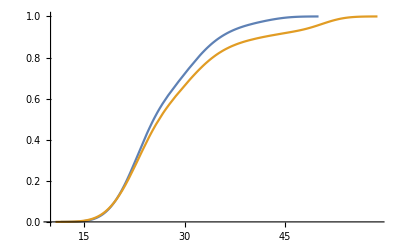

```mathematica
{ansAgeRmOtl,ansAgeRmFarOtl}//SmoothHistogram[#,Automatic,"CDF",AxesOrigin->{10,0}]&
```

分别筛除异常值和严重异常值的结果, 分别显示年龄分布呈正偏特征. 进一步分析: 部分受访者填写的年龄数据(介于40a至60a)可能非异常值. 
可能原因推测: 多数(近80%)受访者年龄在20~40岁之间, 少数(近10%)位于40~60岁之间, 考虑到问卷通过网络发布和填写, 这一分布特征与移动互联网用户的年龄特征吻合程度较好.

#### 2.1.3. 职业分布

问卷涉及的职业主要分为以下大类:

学生;

工农生产行业;

机关单位职工;

R&D行业工作者;

其他事业单位职工;

企业职工和商贸工作者;

自由职业者;

离退休人员.

```mathematica
career={
	"Arb","Arb","Gov","Stu","Prac","Prac","Prac","RD","Prac","Biz",
	"Biz","RD","Biz","Biz","Biz","Biz","Unemp","Ret"
};
```

```mathematica
ansCar=Part[career,#]&/@ansRaw[[2;;,10]];
```

```mathematica
Tally[ansCar]//Sort[#,#1[[2]]≥#2[[2]]&]&
```

{{Stu,33},{Biz,13},{Gov,10},{Prac,6},{RD,6},{Unemp,5},{Arb,5}}

受访者以学生, 企业职工和商贸工作者, 以及机关单位员工为主. 
可能原因推测: 与东湖绿道附近的高校(如WHU, HUST, CUG), 机关单位和企业分布有关.

受访者不包含离退休人员. 
可能原因推测: 网络问卷的调查形式对离退休人员的覆盖能力不足. 
考虑到东湖绿道部分路段周边存在集群的居住区分布(如毕阁山-小李村, 东湖村-沙湾村, 梨园-红庙), 东湖绿道的实际用户中可能包含一定比例的离退休人员, 后续软件开发中, 为调查这些用户的需求, 需要前往东湖绿道不同路段实地走访调查.

### 2.2. 受访者生活与东湖绿道的关系分析

#### 2.2.1. 受访者对地理信息服务的接纳特征

```mathematica
ansGisAcception=ansRaw[[2;;,11;;17]];
```

```mathematica
(ansGisAcception//Total)/78//Round[#,1.*^-3]&
```

{0.654,0.295,0.526,0.641,0.231,0.192,0.192}

所有受访者中, 具有电子地图软件使用经验者, 为户外游览提前规划路线者, 以及户外运动爱好者比例均过半.

分别按性别进行统计

```mathematica
ansGisAcptByGender={1.,2.}/.(MapThread[List[##]&,{ansGender,ansGisAcception}]//GroupBy[#,#[[1]]&]&);
ansGisAcptByGender=ansGisAcptByGender[[All,All,2]];
```

```mathematica
(Total[#,1]&/@ansGisAcptByGender)/(Tally[ansGender][[All,2]])//Round[#,1.*^-3]&
```

{{0.69,0.362,0.603,0.69,0.224,0.241,0.224},{0.55,0.1,0.3,0.5,0.25,0.05,0.1}}

```mathematica
PairedBarChart@@((Total[#,1]&/@ansGisAcptByGender)/(Tally[ansGender][[All,2]]))
```

-Graphics-

男性在户外运动, 地图使用, 户外行程规划的比例均高于女性, 外业工作的比例与女性相近.

```mathematica
Table[(Total[#,1]&/@ansGisAcptByGender)/(Tally[ansGender][[All,2]])//PairedTTest[#,AlternativeHypothesis->H0]&,{H0,{"Unequal","Greater","Less"}}]
```

{0.0057515,0.00287575,0.997124}

男性在地理信息服务方面的需求比例高于女性, 这一差异具有统计显著性, 通过双尾, 单尾成对t-检验(p<0.05).

#### 2.2.2. 受访者工作生活环境与东湖绿道的密切程度

```mathematica
ansELGWAccess=ansRaw[[2;;,19]];
```

```mathematica
ansELGWAccess//Tally//Sort[#,#1[[1]]<#2[[1]]&]&
```

{{1.,20},{2.,7},{3.,22},{4.,20},{5.,9}}

武汉市内居民约占六成. 
据此, 后续问卷分析中,  “工作生活环境与东湖绿道关系”结果中的部分选项将合并为三项:

绿道周边居民(选项1维持不变)

武汉本地其他居民(选项2与3合并)

武汉市外其他地区居民(选项4与5合并)

```mathematica
ansELGWFreq=ansRaw[[2;;,20]];
```

```mathematica
ansELGWFreq//Tally//Sort[#,#1[[1]]<#2[[1]]&]&
```

{{1.,3},{2.,11},{3.,14},{4.,16},{5.,34}}

超过1/6的受访每周到访东湖绿道一次(含)以上; 超过1/3的受访者每月到访东湖绿道一次(含)以上. 
据此, 后续问卷分析中, “东湖绿道到访频率”结果中的部分选项将合并为四项:

## 3. 受访者在东湖绿道游览习惯分析

### 3.1. 东湖绿道游览时间偏好

#### 3.1.1. 受访者在工作日和不同日数休息日的游览时长

问卷涉及的不同日数休息日主要分为以下类别:

周末, 三天小长假(如清明节, 中秋节)

假期多于三天的法定节假日(如春节, 劳动节, 国庆节)

暑假或年假

统计受访者在工作日和三种类型的休息日前往东湖绿道的游览小时数

```mathematica
ansELGWDura=ansRaw[[2;;,41;;44]];
```

```mathematica
Table[stat[ansELGWDura[[All,type]]],{type,4},{stat,{Mean,StandardDeviation,Skewness,Kurtosis}}]//Round[#,1.*^-3]&//TableForm
```

1.692 | 2.034 | 2.575 | 12.734
2.692 | 2.116 | 1.792 | 8.915
2.846 | 2.471 | 1.327 | 5.519
2.474 | 2.459 | 1.854 | 7.773

工作日和三种类型的休息日的游览时长均受异常值影响, 峰度统计结果受极端值影响严重.

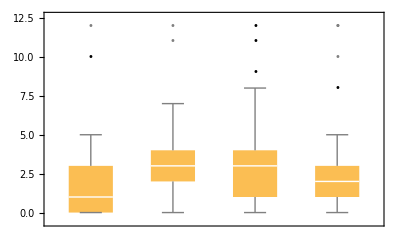

```mathematica
ansELGWDura//Transpose//BoxWhiskerChart[#,"Outliers"]&
```

由于工作日和三种类型的休息日调查结果均存在异常值, 且异常值分布特征相近, 此处仅分析游览时长平均值的差异.

对工作日和三种类型的休息日的游览时长两两比对, 开展成对双尾t-检验:

```mathematica
ParallelTable[ansELGWDura[[All,{type1,type2}]]//Transpose//PairedTTest//Quiet,{type1,4},{type2,4}]//TableForm
```

1. | 0.000116111 | 0.0000720892 | 0.00546048
0.000116111 | 1. | 0.424127 | 0.439896
0.0000720892 | 0.424127 | 1. | 0.147709
0.00546048 | 0.439896 | 0.147709 | 1.

t-检验结果显示: 受访者在工作日的游览时长均值与各类休息日游览时长均值存在差异, 这一差异具有统计显著性(p<0.05); 
不同类型休息日的游览时长均值之间的差异不具备统计显著性(p≥0.05).

分别按性别进行统计

```mathematica
ansELGWDuraByGender={1.,2.}/.(MapThread[List[##]&,{ansGender,ansELGWDura}]//GroupBy[#,#[[1]]&]&);
ansELGWDuraByGender=ansELGWDuraByGender[[All,All,2]];
```

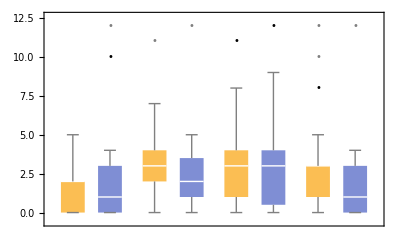

```mathematica
BoxWhiskerChart[MapThread[List,Transpose/@ansELGWDuraByGender],"Outliers"]
```

```mathematica
TTest/@MapThread[List,Transpose/@ansELGWDuraByGender]
```

{0.197473,0.985102,0.671636,0.228015}

男性和女性在工作日和三类休息日的游览时长, 均值之间的差异不具备统计显著性, 未通过双尾t-检验(p≥0.05).

分别按工作生活环境与东湖绿道关系进行统计

```mathematica
ansELGWDuraByAccess=Range[0,2]/.(MapThread[List[##]&,{ansELGWAccess,ansELGWDura}]//GroupBy[#,Quotient[#[[1]],2]&]&);
ansELGWDuraByAccess=ansELGWDuraByAccess[[All,All,2]];
```

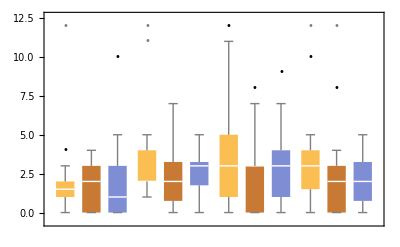

```mathematica
BoxWhiskerChart[MapThread[List,Transpose/@ansELGWDuraByAccess],"Outliers"]
```

```mathematica
Map[Mean,MapThread[List,Transpose/@ansELGWDuraByAccess],{2}]//Transpose//Round[#,1.*^-3]&//TableForm
```

2.05 | 3.4 | 3.5 | 3.45
1.483 | 2.414 | 2.483 | 2.138
1.655 | 2.483 | 2.759 | 2.138

以居住地类型为单位, 对工作日和三种类型的休息日的游览时长两两比对, 开展成对双尾t-检验:

```mathematica
ParallelTable[citizen[[All,{type1,type2}]]//Transpose//PairedTTest//Quiet,{citizen,ansELGWDuraByAccess},{type1,4},{type2,4}]//TableForm
```

1.
0.0195813
0.0213465
0.0187617 | 0.0195813
1.
0.827446
0.943614 | 0.0213465
0.827446
1.
0.938408 | 0.0187617
0.943614
0.938408
1.
1.
0.0306852
0.0558476
0.184799 | 0.0306852
1.
0.798024
0.606577 | 0.0558476
0.798024
1.
0.429977 | 0.184799
0.606577
0.429977
1.
1.
0.0386716
0.00787655
0.250181 | 0.0386716
1.
0.397772
0.20962 | 0.00787655
0.397772
1.
0.0561917 | 0.250181
0.20962
0.0561917
1.

针对不同地区居民的t - 检验结果显示:

对于东湖绿道周边居民, 在工作日的游览时长均值与各类休息日游览时长均值存在差异, 这一差异具有统计显著性(p<0.05); 
不同类型休息日的游览时长均值之间的差异不具备统计显著性(p≥0.05); 
上述特征与全体问卷受访者的游览时长差异特征一致.

对于武汉本地其他居民, 在工作日的游览时长与周末或三天小长假的游览时长均值存在显著性差异(p<0.05); 
工作日与长假的游览时长均值之间, 以及不同类型休息日的游览时长均值之间, 差异均不具备统计显著性(p≥0.05);

对于武汉以外其他地区居民, 在工作日的游览时长与周末, 节假日的游览时长均值存在显著性差异(p<0.05);

工作日的游览时长最低, 暑假或年假期间的游览时长其次, 其他法定节假日的游览时长较高.

对于假期天数少于或多于三天的法定节假日, 游览时长均值之间的差异不具备统计显著性(p≥0.05).

可能原因推测:

工作日<法定节假日: 受访者在工作日的闲暇时间较节假日少;

法定节假日>暑假或年假: 部分受访者在暑假或年假期间优先选择前往其他景点旅游, 相对于武汉本地居民, 该现象在武汉市以外居民中的体现更加集中.

#### 3.1.2. 受访者在工作日和不同日数休息日的游览时段分布

```mathematica
ansELGWPhase=ansRaw[[2;;,21;;40]];
```

```mathematica
ansELGWPhase//Total[#,1]&//Divide[#,78]&//Partition[#,5]&//Part[#,All,;;-2]&//Round[#,1.*^-3]&//TableForm
```

0.038 | 0.128 | 0.244 | 0.359
0.064 | 0.256 | 0.5 | 0.308
0.051 | 0.269 | 0.449 | 0.256
0.038 | 0.269 | 0.372 | 0.321

工作日期间, 受访者在晚间前往东湖绿道的比例较高, 下午次之, 上午再次之; 周末和节假日期间, 受访者在下午时段前往东湖绿道的比例较高, 晚间和上午次之. 受访者在节假日白天前往东湖绿道的比例较工作日白天更高.